```mathematica
Integrate[D[Sin[10*Pi*x],x]^2+Sin[10*Pi*x]^2,{x,0,1}]
```

1/2+50 π^2

```mathematica
N[1/2+50 π^2]
```

493.98

```mathematica
DSolve[-u''[x]+u[x]==1,u[x],x]
```

{{u[x]→1+ⅇ^x C[1]+ⅇ^-x C[2]}}

```mathematica
u[x_]:=1+ⅇ^x C[1]+ⅇ^-x C[2]
```

```mathematica
u[x]
```

1+ⅇ^x C[1]+ⅇ^-x C[2]

```mathematica
Solve[u[0]==0&&u[1]==0,{C[1], C[2]}]
```

{{C[1]→-1/(1+ⅇ),C[2]→-ⅇ/(1+ⅇ)}}

```mathematica
u[x_]:=1+ⅇ^x *(-1/(1+ⅇ))+ⅇ^-x *(-ⅇ/(1+ⅇ))
```

```mathematica
u[x]
```

1-ⅇ^(1-x)/(1+ⅇ)-ⅇ^x/(1+ⅇ)

```mathematica
u[0]
```

1-1/(1+ⅇ)-ⅇ/(1+ⅇ)

```mathematica
N[1-1/(1+ⅇ)-ⅇ/(1+ⅇ)]
```

1.11022×10^-16

```mathematica
u[1]
```

1-1/(1+ⅇ)-ⅇ/(1+ⅇ)

```mathematica
N[1-1/(1+ⅇ)-ⅇ/(1+ⅇ)]
```

1.11022×10^-16

{(-1+x) x,(-1+x) x^2,(-1+x) x^3,(-1+x) x^4,(-1+x) x^5,(-1+x) x^6}

{{0.39328,0.19664,0.135712,0.105248,0.0901972,0.0828531},{0.19664,0.168992,0.138528,0.118613,0.106405,0.0990774},{0.135712,0.138528,0.128085,0.118181,0.110757,0.1056},{0.105248,0.118613,0.118181,0.11465,0.110986,0.107953},{0.0901972,0.106405,0.110757,0.110986,0.10988,0.108471},{0.0828531,0.0990774,0.1056,0.107953,0.108471,0.10819}}

{-0.16,-0.08,-0.04672,-0.03008,-0.020608,-0.01472}

{-0.209465,-9.08294,39.9514,-61.737,30.8685,7.79901×10^-10}

{{11/30,11/60,23/210,61/840,13/252,97/2520},{11/60,1/7,89/840,101/1260,157/2520,172/3465},{23/210,89/840,113/1260,187/2520,853/13860,17/330},{61/840,101/1260,187/2520,227/3465,113/1980,71/1430},{13/252,157/2520,853/13860,113/1980,133/2574,557/12012},{97/2520,172/3465,17/330,71/1430,557/12012,641/15015}}

{-1/6,-1/12,-1/20,-1/30,-1/42,-1/56}

{-159417/344971,108/2851,-1227/31361,78/31361,-39/31361,0}

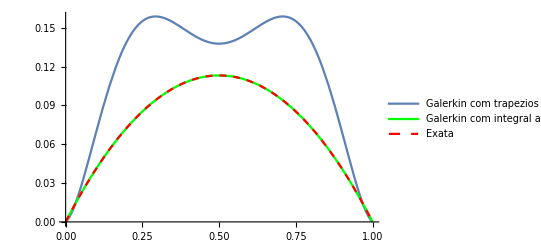

```mathematica
Tn[f_,a_,b_,m_]:=0.5*((b-a)/m)*(f[a]+f[b]+Sum[2*f[a+(i*(b-a))/m],{i,1,m-1}])
ϕ=Table[x^i*(x-1),{i,1,6}]
K=Table[Tn[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]]/.x->#&,0,1,5],{j,6},{n,6}]
F=Table[Tn[ϕ[[j]]/.x->#&,0,1,5],{j,1,6}]
W=LinearSolve[K,F]
Uh[x_]:=W.ϕ
k=Table[Integrate[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]],{x,0,1}],{j,6},{n,6}]
f=Table[Integrate[ϕ[[j]],{x,0,1}],{j,1,6}]
w=LinearSolve[k,f]
uh[x_]:=w.ϕ

G66=Plot[{Uh[x],uh[x],u[x]},{x,0,1},PlotStyle->{,Green,{Red,Dashed}},PlotLegends->{"Galerkin com trapezios compostos","Galerkin com integral analítica","Exata"},ImageSize->400,AxesStyle->Black]
```

```mathematica
Export["ah_n_6.png",G66]
```

ah_n_6.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["ah_n_6.png"]]]
```

{(-1+x) x,(-1+x) x^2,(-1+x) x^3,(-1+x) x^4,(-1+x) x^5,(-1+x) x^6,(-1+x) x^7,(-1+x) x^8,(-1+x) x^9,(-1+x) x^10}

{{0.366733,0.183367,0.10959,0.0727024,0.0516873,0.0386087,0.0299313,0.0238873,0.0195139,0.0162505},{0.183367,0.142924,0.106036,0.0802587,0.0624182,0.0497726,0.040554,0.0336553,0.0283717,0.0242425},{0.10959,0.106036,0.0897825,0.074323,0.0616773,0.0516651,0.0437564,0.0374626,0.032401,0.0282843},{0.0727024,0.0802587,0.074323,0.0656456,0.0572207,0.049817,0.0435232,0.0382285,0.0337788,0.0300274},{0.0516873,0.0624182,0.0616773,0.0572207,0.0518372,0.0465536,0.041725,0.0374418,0.0336904,0.0304202},{0.0386087,0.0497726,0.0516651,0.049817,0.0465536,0.0428905,0.0392733,0.0358882,0.0328011,0.0300222},{0.0299313,0.040554,0.0437564,0.0435232,0.041725,0.0392733,0.0366208,0.0339916,0.0314928,0.0291702},{0.0238873,0.0336553,0.0374626,0.0382285,0.0374418,0.0358882,0.0339916,0.031983,0.0299872,0.02807},{0.0195139,0.0283717,0.032401,0.0337788,0.0336904,0.0328011,0.0314928,0.0299872,0.028414,0.0268485},{0.0162505,0.0242425,0.0282843,0.0300274,0.0304202,0.0300222,0.0291702,0.02807,0.0268485,0.0255837}}

{-0.16665,-0.083325,-0.0499917,-0.033325,-0.0238012,-0.0178488,-0.0138806,-0.0111028,-0.00908258,-0.00756743}

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.366733,0.183367,0.10959,0.0727024,0.0516873,0.0386087,0.0299313,0.0238873,0.0195139,0.0162505},«8»,{0.0162505,0.0242425,0.0282843,0.0300274,0.0304202,0.0300222,0.0291702,0.02807,0.0268485,0.0255837}} may contain significant numerical errors.

{-0.439972,-0.726172,9.30544,-56.0203,186.659,-362.563,407.829,-245.978,61.4948,-0.0000936298}

{{11/30,11/60,23/210,61/840,13/252,97/2520,59/1980,47/1980,83/4290,193/12012},{11/60,1/7,89/840,101/1260,157/2520,172/3465,4/99,431/12870,1693/60060,361/15015},{23/210,89/840,113/1260,187/2520,853/13860,17/330,17/390,2239/60060,967/30030,613/21840},{61/840,101/1260,187/2520,227/3465,113/1980,71/1430,2603/60060,571/15015,733/21840,5531/185640},{13/252,157/2520,853/13860,113/1980,133/2574,557/12012,1247/30030,271/7280,6211/185640,517/17136},{97/2520,172/3465,17/330,71/1430,557/12012,641/15015,853/21840,6619/185640,2789/85680,173/5814},{59/1980,4/99,17/390,2603/60060,1247/30030,853/21840,193/5304,413/12240,3631/116280,3359/116280},{47/1980,431/12870,2239/60060,571/15015,271/7280,6619/185640,413/12240,461/14535,1727/58140,5651/203490},{83/4290,1693/60060,967/30030,733/21840,6211/185640,2789/85680,3631/116280,1727/58140,1907/67830,2329/87780},{193/12012,361/15015,613/21840,5531/185640,517/17136,173/5814,3359/116280,5651/203490,2329/87780,2549/100947}}

{-1/6,-1/12,-1/20,-1/30,-1/42,-1/56,-1/72,-1/90,-1/110,-1/132}

{-110501920685/239121008491,9058583560/239121008491,-9358403210/239121008491,604972030/239121008491,-315876626/239121008491,16233334/239121008491,-5685446/239121008491,235144/239121008491,-58786/239121008491,0}

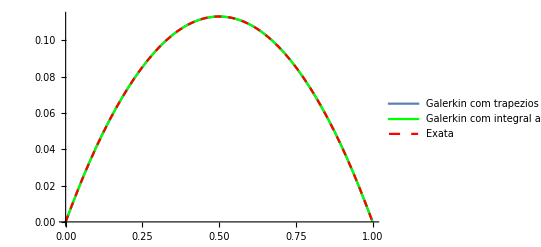

```mathematica
Tn[f_,a_,b_,m_]:=0.5*((b-a)/m)*(f[a]+f[b]+Sum[2*f[a+(i*(b-a))/m],{i,1,m-1}])
ϕ=Table[x^i*(x-1),{i,1,10}]
K=Table[Tn[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]]/.x->#&,0,1,100],{j,10},{n,10}]
F=Table[Tn[ϕ[[j]]/.x->#&,0,1,100],{j,1,10}]
W=LinearSolve[K,F]
Uh[x_]:=W.ϕ
k=Table[Integrate[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]],{x,0,1}],{j,10},{n,10}]
f=Table[Integrate[ϕ[[j]],{x,0,1}],{j,1,10}]
w=LinearSolve[k,f]
uh[x_]:=w.ϕ

G56=Plot[{Uh[x],uh[x],u[x]},{x,0,1},PlotStyle->{,Green,{Red,Dashed}},PlotLegends->{"Galerkin com trapezios compostos","Galerkin com integral analítica","Exata"},ImageSize->400,AxesStyle->Black]
```

```mathematica
Export["ah_n_10.png",G56]
```

ah_n_10.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["ah_n_10.png"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["ah_n_6.png"]]]
```

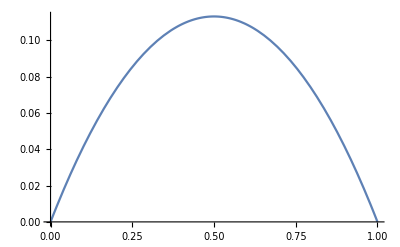

```mathematica
Plot[1+ⅇ^x *(-1/(1+ⅇ))+ⅇ^-x *(-ⅇ/(1+ⅇ)),{x,0,1}]
```

{(-1+x) x,(-1+x) x^2,(-1+x) x^3,(-1+x) x^4,(-1+x) x^5,(-1+x) x^6}

{{0.0332836,0.0166418,0.00947326,0.00588899,0.00389411,0.00269392},{0.0166418,0.0094736,0.00588933,0.0038944,0.00269416,0.00192814},{0.00947326,0.00588933,0.00389449,0.00269427,0.00192826,0.00141621},{0.00588899,0.0038944,0.00269427,0.0019283,0.00141626,0.00106112},{0.00389411,0.00269416,0.00192826,0.00141626,0.00106114,0.000807389},{0.00269392,0.00192814,0.00141621,0.00106112,0.000807389,0.000621697}}

{-0.16,-0.08,-0.04672,-0.03008,-0.020608,-0.01472}

{-1.47718,-67.071,299.844,-465.547,232.773,-3.75353×10^-7}

{{10001/300000,10001/600000,200021/21000000,62507/10500000,25003/6300000,70009/25200000},{10001/600000,16669/1750000,125021/21000000,3907/984375,14003/5040000,140033/69300000},{200021/21000000,125021/21000000,17861/4500000,35009/12600000,112033/55440000,100033/66000000},{62507/10500000,3907/984375,35009/12600000,35011/17325000,30011/19800000,10421/8937500},{25003/6300000,14003/5040000,112033/55440000,30011/19800000,30013/25740000,550273/600600000},{70009/25200000,140033/69300000,100033/66000000,10421/8937500,550273/600600000,110063/150150000}}

{-1/6,-1/12,-1/20,-1/30,-1/42,-1/56}

{-338118943050000/12556294553861,2476608750000000/12556294553861,-7839108750000000/12556294553861,10725000000000000/12556294553861,-5362500000000000/12556294553861,0}

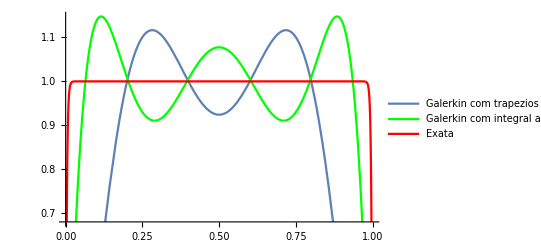

```mathematica
Tn[f_,a_,b_,m_]:=0.5*((b-a)/m)*(f[a]+f[b]+Sum[2*f[a+(i*(b-a))/m],{i,1,m-1}])
ϕ=Table[x^i*(x-1),{i,1,6}]
K=Table[Tn[D[ϕ[[j]],x]*D[ϕ[[n]],x]*10^(-5)+ϕ[[j]]*ϕ[[n]]/.x->#&,0,1,5],{j,6},{n,6}]
F=Table[Tn[ϕ[[j]]/.x->#&,0,1,5],{j,1,6}]
W=LinearSolve[K,F]
Uh[x_]:=W.ϕ
k=Table[Integrate[D[ϕ[[j]],x]*D[ϕ[[n]],x]*10^(-5)+ϕ[[j]]*ϕ[[n]],{x,0,1}],{j,6},{n,6}]
f=Table[Integrate[ϕ[[j]],{x,0,1}],{j,1,6}]
w=LinearSolve[k,f]
uh[x_]:=w.ϕ
u1[x_]:=1+ⅇ^(100 √10 x) *(-1/(1+ⅇ^(100 √10)))+ⅇ^(-100 √10 x) *(-ⅇ^(100 √10)/(1+ⅇ^(100 √10)))

G76=Plot[{Uh[x],uh[x],u1[x]},{x,0,1},PlotStyle->{,Green,{Red}},PlotLegends->{"Galerkin com trapezios compostos","Galerkin com integral analítica","Exata"},ImageSize->400,AxesStyle->Black]
```

```mathematica
Export["bh_n_6.png",G76]
```

bh_n_6.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["bh_n_6.png"]]]
```

{(-1+x) x,(-1+x) x^2,(-1+x) x^3,(-1+x) x^4,(-1+x) x^5,(-1+x) x^6,(-1+x) x^7,(-1+x) x^8,(-1+x) x^9,(-1+x) x^10}

{{0.0333367,0.0166683,0.00952481,0.00595305,0.00396873,0.00277814,0.00202048,0.00151537,0.00116568,0.000915903},{0.0166683,0.00952514,0.00595338,0.00396902,0.00277837,0.00202068,0.00151554,0.00116583,0.000916025,0.000732835},{0.00952481,0.00595338,0.00396911,0.00277849,0.0020208,0.00151565,0.00116593,0.000916115,0.000732916,0.000595514},{0.00595305,0.00396902,0.00277849,0.00202084,0.00151571,0.00116599,0.000916176,0.000732975,0.000595569,0.00049049},{0.00396873,0.00277837,0.0020208,0.00151571,0.00116601,0.000916206,0.00073301,0.000595605,0.000490527,0.000408796},{0.00277814,0.00202068,0.00151565,0.00116599,0.000916206,0.000733021,0.000595624,0.000490549,0.000408819,0.000344293},{0.00202048,0.00151554,0.00116593,0.000916176,0.00073301,0.000595624,0.000490556,0.000408831,0.000344307,0.000292685},{0.00151537,0.00116583,0.000916115,0.000732975,0.000595605,0.000490549,0.000408831,0.000344312,0.000292693,0.000250903},{0.00116568,0.000916025,0.000732916,0.000595569,0.000490527,0.000408819,0.000344307,0.000292693,0.000250907,0.000216715},{0.000915903,0.000732835,0.000595514,0.00049049,0.000408796,0.000344293,0.000292685,0.000250903,0.000216715,0.00018847}}

{-0.16665,-0.083325,-0.0499917,-0.033325,-0.0238012,-0.0178488,-0.0138806,-0.0111028,-0.00908258,-0.00756743}

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.0333367,0.0166683,0.00952481,0.00595305,0.00396873,0.00277814,0.00202048,0.00151537,0.00116568,0.000915903},«8»,{0.000915903,0.000732835,0.000595514,0.00049049,0.000408796,0.000344293,0.000292685,0.000250903,0.000216715,0.00018847}} may contain significant numerical errors.

{-62.5455,1227.88,-11552.5,59607.7,-181475.,333977.,-364620.,217121.,-54291.,4.60658}

{{10001/300000,10001/600000,200021/21000000,62507/10500000,25003/6300000,70009/25200000,80011/39600000,75011/49500000,250039/214500000,550091/600600000},{10001/600000,16669/1750000,125021/21000000,3907/984375,14003/5040000,140033/69300000,300077/198000000,23444/20109375,2750819/3003000000,22007/30030000},{200021/21000000,125021/21000000,17861/4500000,35009/12600000,112033/55440000,100033/66000000,250091/214500000,687773/750750000,440189/600600000,929/1560000},{62507/10500000,3907/984375,35009/12600000,35011/17325000,30011/19800000,10421/8937500,1375637/1501500000,13757/18768750,16259/27300000,56909/116025000},{25003/6300000,14003/5040000,112033/55440000,30011/19800000,30013/25740000,550273/600600000,6773/9240000,271/455000,227653/464100000,70051/171360000},{70009/25200000,140033/69300000,100033/66000000,10421/8937500,550273/600600000,110063/150150000,32521/54600000,284579/580125000,1751377/4284000000,200171/581400000},{80011/39600000,300077/198000000,250091/214500000,1375637/1501500000,6773/9240000,32521/54600000,162619/331500000,62551/153000000,4003591/11628000000,136133/465120000},{75011/49500000,23444/20109375,687773/750750000,13757/18768750,271/455000,284579/580125000,62551/153000000,62557/181687500,170171/581400000,3191/12718125},{250039/214500000,2750819/3003000000,440189/600600000,16259/27300000,227653/464100000,1751377/4284000000,4003591/11628000000,170171/581400000,170189/678300000,190231/877800000},{550091/600600000,22007/30030000,929/1560000,56909/116025000,70051/171360000,200171/581400000,136133/465120000,3191/12718125,190231/877800000,27179/144210000}}

{-1/6,-1/12,-1/20,-1/30,-1/42,-1/56,-1/72,-1/90,-1/110,-1/132}

{-51423533251874541550000/802721763465919415831,1022164640044096250000000/802721763465919415831,-9682556224531596250000000/802721763465919415831,50166804575225000000000000/802721763465919415831,-153125018303237500000000000/802721763465919415831,282244314218750000000000000/802721763465919415831,-308405396406250000000000000/802721763465919415831,183706250000000000000000000/802721763465919415831,-45926562500000000000000000/802721763465919415831,0}

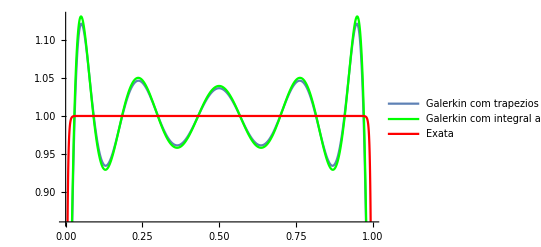

```mathematica
Tn[f_,a_,b_,m_]:=0.5*((b-a)/m)*(f[a]+f[b]+Sum[2*f[a+(i*(b-a))/m],{i,1,m-1}])
ϕ=Table[x^i*(x-1),{i,1,10}]
K=Table[Tn[D[ϕ[[j]],x]*D[ϕ[[n]],x]*10^(-5)+ϕ[[j]]*ϕ[[n]]/.x->#&,0,1,100],{j,10},{n,10}]
F=Table[Tn[ϕ[[j]]/.x->#&,0,1,100],{j,1,10}]
W=LinearSolve[K,F]
Uh[x_]:=W.ϕ
k=Table[Integrate[D[ϕ[[j]],x]*D[ϕ[[n]],x]*10^(-5)+ϕ[[j]]*ϕ[[n]],{x,0,1}],{j,10},{n,10}]
f=Table[Integrate[ϕ[[j]],{x,0,1}],{j,1,10}]
w=LinearSolve[k,f]
uh[x_]:=w.ϕ
u1[x_]:=1+ⅇ^(100 √10 x) *(-1/(1+ⅇ^(100 √10)))+ⅇ^(-100 √10 x) *(-ⅇ^(100 √10)/(1+ⅇ^(100 √10)))

G76=Plot[{Uh[x],uh[x],u1[x]},{x,0,1},PlotStyle->{,Green,{Red}},PlotLegends->{"Galerkin com trapezios compostos","Galerkin com integral analítica","Exata"},ImageSize->400,AxesStyle->Black]
```

```mathematica
Export["bh_n_10.png",G76]
```

bh_n_10.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["bh_n_10.png"]]]
```

{(-1+x) x,(-1+x) x^2,(-1+x) x^3,(-1+x) x^4,(-1+x) x^5,(-1+x) x^6}

{{0.39328,0.19664,0.135712,0.105248,0.0901972,0.0828531},{0.19664,0.168992,0.138528,0.118613,0.106405,0.0990774},{0.135712,0.138528,0.128085,0.118181,0.110757,0.1056},{0.105248,0.118613,0.118181,0.11465,0.110986,0.107953},{0.0901972,0.106405,0.110757,0.110986,0.10988,0.108471},{0.0828531,0.0990774,0.1056,0.107953,0.108471,0.10819}}

{-0.08,-0.04672,-0.03008,-0.020608,-0.01472,-0.0108268}

{-0.11044,-0.152526,-9.45126,43.0641,-66.0377,32.5888}

{{11/30,11/60,23/210,61/840,13/252,97/2520},{11/60,1/7,89/840,101/1260,157/2520,172/3465},{23/210,89/840,113/1260,187/2520,853/13860,17/330},{61/840,101/1260,187/2520,227/3465,113/1980,71/1430},{13/252,157/2520,853/13860,113/1980,133/2574,557/12012},{97/2520,172/3465,17/330,71/1430,557/12012,641/15015}}

{-1/12,-1/20,-1/30,-1/42,-1/56,-1/72}

{-191546527697/1284841384761,-1583036137/10618523841,-847653557/116803762251,-283443719/38934587417,-16569787/116803762251,-715/3724491}

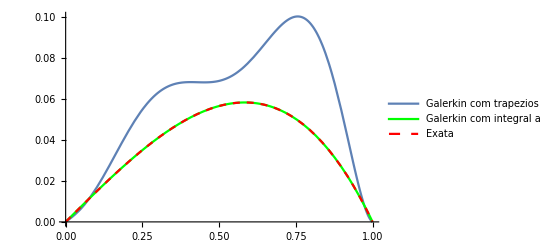

```mathematica
Tn[f_,a_,b_,m_]:=0.5*((b-a)/m)*(f[a]+f[b]+Sum[2*f[a+(i*(b-a))/m],{i,1,m-1}])
ϕ=Table[x^i*(x-1),{i,1,6}]
K=Table[Tn[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]]/.x->#&,0,1,5],{j,6},{n,6}]
F=Table[Tn[ϕ[[j]]*x/.x->#&,0,1,5],{j,1,6}]
W=LinearSolve[K,F]
Uh[x_]:=W.ϕ
k=Table[Integrate[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]],{x,0,1}],{j,6},{n,6}]
f=Table[Integrate[ϕ[[j]]*x,{x,0,1}],{j,1,6}]
w=LinearSolve[k,f]
uh[x_]:=w.ϕ
u2[x_]:=x+ⅇ^x *(-ⅇ/(-1+ⅇ^2))+ⅇ^-x *(ⅇ/(-1+ⅇ^2))

G46=Plot[{Uh[x],uh[x],u2[x]},{x,0,1},PlotStyle->{,Green,{Red,Dashed}},PlotLegends->{"Galerkin com trapezios compostos","Galerkin com integral analítica","Exata"},ImageSize->400,AxesStyle->Black]
```

```mathematica
Export["an_n_6.png",G46]
```

an_n_6.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["an_n_6.png"]]]
```

{(-1+x) x,(-1+x) x^2,(-1+x) x^3,(-1+x) x^4,(-1+x) x^5,(-1+x) x^6,(-1+x) x^7,(-1+x) x^8,(-1+x) x^9,(-1+x) x^10}

{{0.366733,0.183367,0.10959,0.0727024,0.0516873,0.0386087,0.0299313,0.0238873,0.0195139,0.0162505},{0.183367,0.142924,0.106036,0.0802587,0.0624182,0.0497726,0.040554,0.0336553,0.0283717,0.0242425},{0.10959,0.106036,0.0897825,0.074323,0.0616773,0.0516651,0.0437564,0.0374626,0.032401,0.0282843},{0.0727024,0.0802587,0.074323,0.0656456,0.0572207,0.049817,0.0435232,0.0382285,0.0337788,0.0300274},{0.0516873,0.0624182,0.0616773,0.0572207,0.0518372,0.0465536,0.041725,0.0374418,0.0336904,0.0304202},{0.0386087,0.0497726,0.0516651,0.049817,0.0465536,0.0428905,0.0392733,0.0358882,0.0328011,0.0300222},{0.0299313,0.040554,0.0437564,0.0435232,0.041725,0.0392733,0.0366208,0.0339916,0.0314928,0.0291702},{0.0238873,0.0336553,0.0374626,0.0382285,0.0374418,0.0358882,0.0339916,0.031983,0.0299872,0.02807},{0.0195139,0.0283717,0.032401,0.0337788,0.0336904,0.0328011,0.0314928,0.0299872,0.028414,0.0268485},{0.0162505,0.0242425,0.0282843,0.0300274,0.0304202,0.0300222,0.0291702,0.02807,0.0268485,0.0255837}}

{-0.083325,-0.0499917,-0.033325,-0.0238012,-0.0178488,-0.0138806,-0.0111028,-0.00908258,-0.00756743,-0.00640193}

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.366733,0.183367,0.10959,0.0727024,0.0516873,0.0386087,0.0299313,0.0238873,0.0195139,0.0162505},«8»,{0.0162505,0.0242425,0.0282843,0.0300274,0.0304202,0.0300222,0.0291702,0.02807,0.0268485,0.0255837}} may contain significant numerical errors.

{-0.143975,-0.286041,1.01723,-0.88268,-21.7595,114.301,-263.753,322.231,-202.953,51.9334}

{{11/30,11/60,23/210,61/840,13/252,97/2520,59/1980,47/1980,83/4290,193/12012},{11/60,1/7,89/840,101/1260,157/2520,172/3465,4/99,431/12870,1693/60060,361/15015},{23/210,89/840,113/1260,187/2520,853/13860,17/330,17/390,2239/60060,967/30030,613/21840},{61/840,101/1260,187/2520,227/3465,113/1980,71/1430,2603/60060,571/15015,733/21840,5531/185640},{13/252,157/2520,853/13860,113/1980,133/2574,557/12012,1247/30030,271/7280,6211/185640,517/17136},{97/2520,172/3465,17/330,71/1430,557/12012,641/15015,853/21840,6619/185640,2789/85680,173/5814},{59/1980,4/99,17/390,2603/60060,1247/30030,853/21840,193/5304,413/12240,3631/116280,3359/116280},{47/1980,431/12870,2239/60060,571/15015,271/7280,6619/185640,413/12240,461/14535,1727/58140,5651/203490},{83/4290,1693/60060,967/30030,733/21840,6211/185640,2789/85680,3631/116280,1727/58140,1907/67830,2329/87780},{193/12012,361/15015,613/21840,5531/185640,517/17136,173/5814,3359/116280,5651/203490,2329/87780,2549/100947}}

{-1/12,-1/20,-1/30,-1/42,-1/56,-1/72,-1/90,-1/110,-1/132,-1/156}

{-153406638324145908741405/1029009339045766393936601,-153406638325161953388085/1029009339045766393936601,-7472854849783359519310/1029009339045766393936601,-7472855075438696828110/1029009339045766393936601,-176164571261162672470/1029009339045766393936601,-176169435167891318806/1029009339045766393936601,-2427272525403134866/1029009339045766393936601,-2444934351873360466/1029009339045766393936601,-14571796761019666/1029009339045766393936601,-104006/4303299595211}

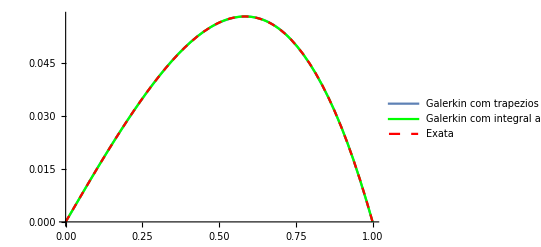

```mathematica
Tn[f_,a_,b_,m_]:=0.5*((b-a)/m)*(f[a]+f[b]+Sum[2*f[a+(i*(b-a))/m],{i,1,m-1}])
ϕ=Table[x^i*(x-1),{i,1,10}]
K=Table[Tn[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]]/.x->#&,0,1,100],{j,10},{n,10}]
F=Table[Tn[ϕ[[j]]*x/.x->#&,0,1,100],{j,1,10}]
W=LinearSolve[K,F]
Uh[x_]:=W.ϕ
k=Table[Integrate[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]],{x,0,1}],{j,10},{n,10}]
f=Table[Integrate[ϕ[[j]]*x,{x,0,1}],{j,1,10}]
w=LinearSolve[k,f]
uh[x_]:=w.ϕ
u2[x_]:=x+ⅇ^x *(-ⅇ/(-1+ⅇ^2))+ⅇ^-x *(ⅇ/(-1+ⅇ^2))

G36=Plot[{Uh[x],uh[x],u2[x]},{x,0,1},PlotStyle->{,Green,{Red,Dashed}},PlotLegends->{"Galerkin com trapezios compostos","Galerkin com integral analítica","Exata"},ImageSize->400,AxesStyle->Black]
```

```mathematica
Export["an_n_10.png",G36]
```

an_n_10.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["an_n_10.png"]]]
```

{(-1+x) x,(-1+x) x^2,(-1+x) x^3,(-1+x) x^4,(-1+x) x^5,(-1+x) x^6}

{{0.0332836,0.0166418,0.00947326,0.00588899,0.00389411,0.00269392},{0.0166418,0.0094736,0.00588933,0.0038944,0.00269416,0.00192814},{0.00947326,0.00588933,0.00389449,0.00269427,0.00192826,0.00141621},{0.00588899,0.0038944,0.00269427,0.0019283,0.00141626,0.00106112},{0.00389411,0.00269416,0.00192826,0.00141626,0.00106114,0.000807389},{0.00269392,0.00192814,0.00141621,0.00106112,0.000807389,0.000621697}}

{-0.08,-0.04672,-0.03008,-0.020608,-0.01472,-0.0108268}

{-0.694226,7.15357,-106.944,386.913,-556.276,269.065}

{{10001/300000,10001/600000,200021/21000000,62507/10500000,25003/6300000,70009/25200000},{10001/600000,16669/1750000,125021/21000000,3907/984375,14003/5040000,140033/69300000},{200021/21000000,125021/21000000,17861/4500000,35009/12600000,112033/55440000,100033/66000000},{62507/10500000,3907/984375,35009/12600000,35011/17325000,30011/19800000,10421/8937500},{25003/6300000,14003/5040000,112033/55440000,30011/19800000,30013/25740000,550273/600600000},{70009/25200000,140033/69300000,100033/66000000,10421/8937500,550273/600600000,110063/150150000}}

{-1/12,-1/20,-1/30,-1/42,-1/56,-1/72}

{93611047348288814020850000/31632822233459434331563749,-2412991526651711185979150000/31632822233459434331563749,14828499024985761354250000000/31632822233459434331563749,-13455430355004746215250000000/10544274077819811443854583,49356121682973462500000000000/31632822233459434331563749,-1787500000000000/2519280039009}

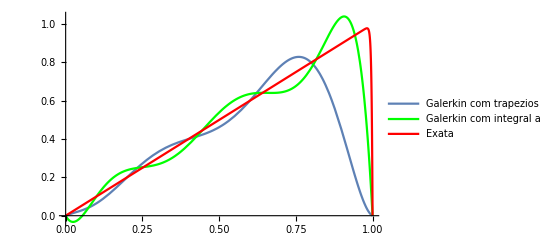

```mathematica
Tn[f_,a_,b_,m_]:=0.5*((b-a)/m)*(f[a]+f[b]+Sum[2*f[a+(i*(b-a))/m],{i,1,m-1}])
ϕ=Table[x^i*(x-1),{i,1,6}]
K=Table[Tn[D[ϕ[[j]],x]*D[ϕ[[n]],x]*10^(-5)+ϕ[[j]]*ϕ[[n]]/.x->#&,0,1,5],{j,6},{n,6}]
F=Table[Tn[ϕ[[j]]*x/.x->#&,0,1,5],{j,1,6}]
W=LinearSolve[K,F]
Uh[x_]:=W.ϕ
k=Table[Integrate[D[ϕ[[j]],x]*D[ϕ[[n]],x]*10^(-5)+ϕ[[j]]*ϕ[[n]],{x,0,1}],{j,6},{n,6}]
f=Table[Integrate[ϕ[[j]]*x,{x,0,1}],{j,1,6}]
w=LinearSolve[k,f]
uh[x_]:=w.ϕ
u3[x_]:=x+ⅇ^(100 √10 x)*(-ⅇ^(100 √10)/(-1+ⅇ^(200 √10)))+ⅇ^(-100 √10 x)*(ⅇ^(100 √10)/(-1+ⅇ^(200 √10)))

G26=Plot[{Uh[x],uh[x],u3[x]},{x,0,1},PlotStyle->{,Green,{Red}},PlotLegends->{"Galerkin com trapezios compostos","Galerkin com integral analítica","Exata"},ImageSize->400,AxesStyle->Black]
```

```mathematica
Export["bn_n_6.png",G26]
```

bn_n_6.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["bn_n_6.png"]]]
```

{(-1+x) x,(-1+x) x^2,(-1+x) x^3,(-1+x) x^4,(-1+x) x^5,(-1+x) x^6,(-1+x) x^7,(-1+x) x^8,(-1+x) x^9,(-1+x) x^10}

{{0.0333367,0.0166683,0.00952481,0.00595305,0.00396873,0.00277814,0.00202048,0.00151537,0.00116568,0.000915903},{0.0166683,0.00952514,0.00595338,0.00396902,0.00277837,0.00202068,0.00151554,0.00116583,0.000916025,0.000732835},{0.00952481,0.00595338,0.00396911,0.00277849,0.0020208,0.00151565,0.00116593,0.000916115,0.000732916,0.000595514},{0.00595305,0.00396902,0.00277849,0.00202084,0.00151571,0.00116599,0.000916176,0.000732975,0.000595569,0.00049049},{0.00396873,0.00277837,0.0020208,0.00151571,0.00116601,0.000916206,0.00073301,0.000595605,0.000490527,0.000408796},{0.00277814,0.00202068,0.00151565,0.00116599,0.000916206,0.000733021,0.000595624,0.000490549,0.000408819,0.000344293},{0.00202048,0.00151554,0.00116593,0.000916176,0.00073301,0.000595624,0.000490556,0.000408831,0.000344307,0.000292685},{0.00151537,0.00116583,0.000916115,0.000732975,0.000595605,0.000490549,0.000408831,0.000344312,0.000292693,0.000250903},{0.00116568,0.000916025,0.000732916,0.000595569,0.000490527,0.000408819,0.000344307,0.000292693,0.000250907,0.000216715},{0.000915903,0.000732835,0.000595514,0.00049049,0.000408796,0.000344293,0.000292685,0.000250903,0.000216715,0.00018847}}

{-0.083325,-0.0499917,-0.033325,-0.0238012,-0.0178488,-0.0138806,-0.0111028,-0.00908258,-0.00756743,-0.00640193}

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.0333367,0.0166683,0.00952481,0.00595305,0.00396873,0.00277814,0.00202048,0.00151537,0.00116568,0.000915903},«8»,{0.000915903,0.000732835,0.000595514,0.00049049,0.000408796,0.000344293,0.000292685,0.000250903,0.000216715,0.00018847}} may contain significant numerical errors.

{4.1926,-239.362,3886.55,-31433.8,144184.,-399088.,678654.,-692937.,389485.,-92582.1}

{{10001/300000,10001/600000,200021/21000000,62507/10500000,25003/6300000,70009/25200000,80011/39600000,75011/49500000,250039/214500000,550091/600600000},{10001/600000,16669/1750000,125021/21000000,3907/984375,14003/5040000,140033/69300000,300077/198000000,23444/20109375,2750819/3003000000,22007/30030000},{200021/21000000,125021/21000000,17861/4500000,35009/12600000,112033/55440000,100033/66000000,250091/214500000,687773/750750000,440189/600600000,929/1560000},{62507/10500000,3907/984375,35009/12600000,35011/17325000,30011/19800000,10421/8937500,1375637/1501500000,13757/18768750,16259/27300000,56909/116025000},{25003/6300000,14003/5040000,112033/55440000,30011/19800000,30013/25740000,550273/600600000,6773/9240000,271/455000,227653/464100000,70051/171360000},{70009/25200000,140033/69300000,100033/66000000,10421/8937500,550273/600600000,110063/150150000,32521/54600000,284579/580125000,1751377/4284000000,200171/581400000},{80011/39600000,300077/198000000,250091/214500000,1375637/1501500000,6773/9240000,32521/54600000,162619/331500000,62551/153000000,4003591/11628000000,136133/465120000},{75011/49500000,23444/20109375,687773/750750000,13757/18768750,271/455000,284579/580125000,62551/153000000,62557/181687500,170171/581400000,3191/12718125},{250039/214500000,2750819/3003000000,440189/600600000,16259/27300000,227653/464100000,1751377/4284000000,4003591/11628000000,170171/581400000,170189/678300000,190231/877800000},{550091/600600000,22007/30030000,929/1560000,56909/116025000,70051/171360000,200171/581400000,136133/465120000,3191/12718125,190231/877800000,27179/144210000}}

{-1/12,-1/20,-1/30,-1/42,-1/56,-1/72,-1/90,-1/110,-1/132,-1/156}

{3061665536649451959861935736141633952650000/651507974382431007197213614718903510107841,-170803470890297362102638064263858366047350000/651507974382431007197213614718903510107841,2769861898116645365107142783411766013250000000/651507974382431007197213614718903510107841,-22365712212154936913017857216588233986750000000/651507974382431007197213614718903510107841,102426370699758132356687162411533662500000000000/651507974382431007197213614718903510107841,-283052234849031763600812837588466337500000000000/651507974382431007197213614718903510107841,480553837808434649143132705558906250000000000000/651507974382431007197213614718903510107841,-489858808562883014255617294441093750000000000000/651507974382431007197213614718903510107841,274874534841261123407094542187500000000000000000/651507974382431007197213614718903510107841,-81254687500000000000000000/811623658450979092711}

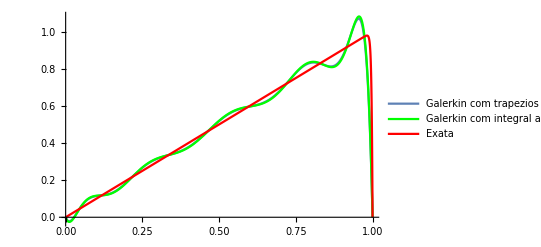

```mathematica
Tn[f_,a_,b_,m_]:=0.5*((b-a)/m)*(f[a]+f[b]+Sum[2*f[a+(i*(b-a))/m],{i,1,m-1}])
ϕ=Table[x^i*(x-1),{i,1,10}]
K=Table[Tn[D[ϕ[[j]],x]*D[ϕ[[n]],x]*10^(-5)+ϕ[[j]]*ϕ[[n]]/.x->#&,0,1,100],{j,10},{n,10}]
F=Table[Tn[ϕ[[j]]*x/.x->#&,0,1,100],{j,1,10}]
W=LinearSolve[K,F]
Uh[x_]:=W.ϕ
k=Table[Integrate[D[ϕ[[j]],x]*D[ϕ[[n]],x]*10^(-5)+ϕ[[j]]*ϕ[[n]],{x,0,1}],{j,10},{n,10}]
f=Table[Integrate[ϕ[[j]]*x,{x,0,1}],{j,1,10}]
w=LinearSolve[k,f]
uh[x_]:=w.ϕ
u3[x_]:=x+ⅇ^(100 √10 x)*(-ⅇ^(100 √10)/(-1+ⅇ^(200 √10)))+ⅇ^(-100 √10 x)*(ⅇ^(100 √10)/(-1+ⅇ^(200 √10)))

G16=Plot[{Uh[x],uh[x],u3[x]},{x,0,1},PlotStyle->{,Green,{Red}},PlotLegends->{"Galerkin com trapezios compostos","Galerkin com integral analítica","Exata"},ImageSize->400,AxesStyle->Black]
```

```mathematica
Export["bn_n_10.png",G16]
```

bn_n_10.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["bn_n_10.png"]]]
```